# 解冷却方程

```mathematica
Quit[]
```

## 电子在磁场中作同步辐射时会损失能量，能量损失率为 为汤姆逊散射截面; 𝑐为光速; 𝛾为电子洛伦兹因子; 为磁场能量密度；电子能量.

### 冷却方程： 解析解为：,其中

```mathematica
DSolve[γ'[t]==-a γ[t]^2,γ[t],t]
```

{{γ[t]→1/(a t-C[1])}}

#### 解形式上一样，只是没有考虑量纲和初始条件

```mathematica
γsol = DSolve[{γ'[t]==-a γ[t]^2, γ[0]== γ0},γ[t],t](*加入初始条件*)
```

{{γ[t]→γ0/(1+a t γ0)}}

#### 由于是一个与电子运动速度无关的量，所以我们可以将其视为一个常数。下面设a=1，不影响物理上的讨论。

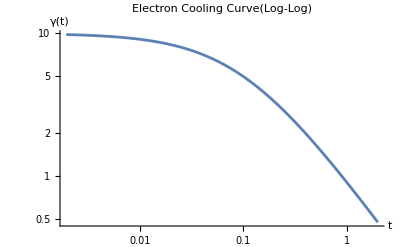

```mathematica
a=1;
γ0=10;
Plot[γ[t] /. γsol[[1]], {t, 0, 2},
AxesLabel->{"t","γ(t)"},
PlotLabel->"Electron Cooling Curve(Log-Log)",
ScalingFunctions->{"Log","Log"},
PlotRange->All]
```

### 可见电子运动会随时间冷却，洛伦兹因子γ随时间减小。

```mathematica
γsol (*这个等式中的a,γ_0已经替换为了1,10*)
```

```mathematica
{{γ[t]->10/(1+10 t)}}
```

{{γ[t]→10/(1+10 t)}}

```mathematica
Quit[]
```

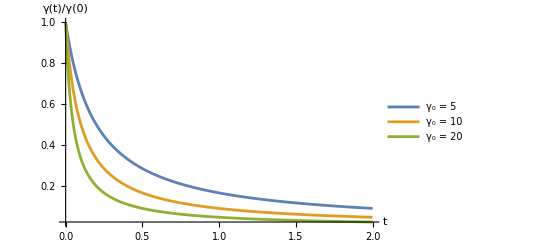

```mathematica
(*看看不同能量电子的冷却速度快慢*)
sol = DSolve[{γ'[t]==-a γ[t]^2, γ[0]== γ0},γ[t],t];
γsol[t_,γ0_]:=γ[t]/. sol[[1]]; 
(*γsol这个函数有两个参数，t和γ0，用DSolve返回的列表的第一个规则‘/.’将γ[t]替换成解析解，用‘:=’SetDelayed延迟赋值（调用时计算）（‘=’Set立即赋值，‘==’Equal等式）*)
a = 1;
γ0list = {5, 10, 20};
Plot[Evaluate@Table[γsol[t,γ0]/γ0,{γ0,γ0list}],{t,0,2},PlotRange->All,AxesLabel->{"t","γ(t)/γ(0)"},PlotLegends->("γ₀ = "<>ToString[#]&/@γ0list)]
```

### 由此可见，能量越高的电子损失能量越快。